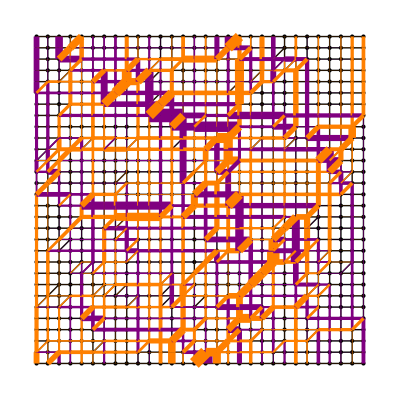
# The Rigidity Package -Graphics-

## Setup and Initialization

The Rigidity package can be loaded by the following (so long as the file “Rigidity.m” is in the same directory as the notebook)

SetDirectory[NotebookDirectory[]]; 
<<"Rigidity.m"

If the file “Rigidity.m” is copied to your Mathematica’s “Application” directory,

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

via the command (uncomment to use),

```mathematica
(*If[Not[FileExistsQ[FileNameJoin[{$UserBaseDirectory,"Applications","Rigidity.m"}]]],CopyFile[FileNameJoin[{NotebookDirectory[],"Rigidity.m"}],FileNameJoin[{$UserBaseDirectory,"Applications","Rigidity.m"}]],Print["Rigidity.m already exists, please replace it manually from "<>ToString[FileNameJoin[{$UserBaseDirectory,"Applications"}]]<> " if you wish to update it."];*)
```

then “<<”Rigidity.m”” can be used in any notebook without any further initialization.

## Basic Operations

### Working with non-periodic frameworks

#### Framework data

A d-dimensional framework consists of a graph G = (V,E), and an embedding of the vertices V into R^d.

The Rigidity package uses adjacency lists to specify the underlying graph of a framework.  Each element of the list corresponds to an edge and contains three pieces of information.  The first is the pair of vertex indices that are joined by the edge.  The second is a labeling of the edge.  For non-periodic graphs, this label will be empty.  The final piece is a dummy slot which could be used to store, e.g. a spring constant.

Here is an example of the edge data for a triangular graph in 2D.

```mathematica
triangleedgedat={{{1,2},{},1},{{2,3},{},1},{{3,1},{},1}};
```

The embedding of the vertices is stored as a list of d-dimensional vectors.

```mathematica
trianglepos={{0,0},{1,0},{0,1}};
```

The function EdgeLengthsSq outputs the squared lengths of each of the edges:

```mathematica
EdgeLengthsSq[trianglepos,{},triangleedgedat]
```

#### Making pictures

The function Draw2DFramework can draw a picture of a 2D framework:

```mathematica
Draw2DFramework[trianglepos,triangleedgedat,{Blue,PointSize->.1},{Thickness->.05}]
```

Similarly, Draw3DFramework makes a picture of a 3D framework:

```mathematica
tetrahedronpos={{0,0,0},{1,0,0},{0,1,0},{0,0,1}};
tetrahedronedgedat={{{1,2},{},1},{{1,3},{},1},{{1,4},{},1},{{2,3},{},1},{{2,4},{},1},{{3,4},{},1}};
Draw3DFramework[tetrahedronpos,tetrahedronedgedat,{Blue,PointSize->.1},{Thickness->.05}]
```

#### Rigidity matrices and drawing modes

The linear rigidity of a framework is completely determined by the properties of the rigidity matrix (often called the compatibility matrix).  This matrix is the Jacobian of the length function on the edges of the framework.

The function RigidityMatrix computes this matrix, as a sparse matrix in Mathematica.  For 2D non-periodic frameworks it should be called as below.  (The empty lists are used only for periodic frameworks, as explained later).

```mathematica
triangleR=RigidityMatrix[{},trianglepos,{},triangleedgedat]
```

```mathematica
Normal[triangleR]//MatrixForm
```

The space of floppy modes and self-stresses can then be computed via linear algebra:

```mathematica
NullSpace[triangleR]
```

```mathematica
NullSpace[Transpose[triangleR]]
```

Here’s an example of computing the rigidity matrix for a 3D non-periodic framework:

```mathematica
tetrahedronR=RigidityMatrix[{},tetrahedronpos,{},tetrahedronedgedat]
```

```mathematica
Normal[tetrahedronR]//MatrixForm
```

The dynamical matrix and hence normal modes can be computed by multiplying the rigidity matrix by its transpose.  
One also needs to sandwich a diagonal matrix whose entries are the physical spring constants divided by the edge lengths squared.

```mathematica
tetrahedronD=Transpose[tetrahedronR].DiagonalMatrix[1/EdgeLengthsSq[tetrahedronpos,{},tetrahedronedgedat]].tetrahedronR;
```

```mathematica
Eigenvalues[tetrahedronD]
tetrahedronModes=Eigenvectors[tetrahedronD];
tetrahedronModes[[1]]
```

The function DynMat is shorthand for this (in fact, it applies a conjugate transpose so that it will work for Fourier-transformed matrices). If the second argument is omitted, the resulting matrix will represent a system whose spring constants are proportional to the squared bond lengths:

```mathematica
tetrahedronD==DynMat[tetrahedronR,DiagonalMatrix[1/EdgeLengthsSq[tetrahedronpos,{},tetrahedronedgedat]]]
```

HMat is a function which computes the class BDI Hamiltonian matrix derived by Kane and Lubensky [KL14] - it just takes the rigidity matrix as input:

```mathematica
HMat[tetrahedronR]
```

The modes (and more generally, any infinitesimal displacements) can be plotted with Draw2DFrameworkMode and Draw3DFrameworkMode, which shows a vector of length dim*numvertices as lines coming off the vertices:

```mathematica
Draw3DFrameworkMode[tetrahedronpos,tetrahedronedgedat,.1tetrahedronModes[[1]],{Blue,PointSize->.06},{Thickness->.02},{Red,Thickness->.02}]
```

Or alternatively with Draw2DFrameworkModeAmp and Draw3DFrameworkModeAmp, which shows the amplitudes of the modes as disks at the vertices:

```mathematica
Draw3DFrameworkModeAmp[tetrahedronpos,tetrahedronedgedat,.1tetrahedronModes[[1]],{Blue,PointSize->.06},{Thickness->.02},{Purple}]
```

Stresses and self-stresses can be drawn as well -- see the section “Plotting stresses and self-stresses” under “Linear response and stresses” in “Other computations”.

### Periodic frameworks

#### Framework data

We will work with three example periodic frameworks, two in 2D, and one in 3D.  In each case, the position data is given as a list of coordinates for the vertices in a single unit cell (fundamental domain).

```mathematica
chainpos={{1,0},{1/2,1/2}};
squarepos={{0,0},{1,0},{0,1},{1,1}};
cubepos={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0},{1,0,1},{0,1,1},{1,1,1}};
```

A periodic framework requires not just the positions of the vertices but also the basis vectors of the lattice.  This is input as a list of d vectors (b_1,...,b_d) for a d-periodic lattice:

```mathematica
chainbasis={{2,0}};
squarebasis={{2,0},{0,2}};
cubebasis={{2,0,0},{0,2,0},{0,0,2}};
```

The edge data of a periodic framework is encoded by giving a list of edges in a unit cell of the lattice.  Each edge is given as a list of three pieces of data:

The first piece is the (now ordered) pair of vertices (p_1,p_2) joined by that edge.

The second piece of data is an integer vector (m_1,...,m_d) (called the “coloring” γ_ij in [MT12] and the “exponent” δ(e) in [P13]) which tells us if an edge wraps the periodic bounary conditions or not, so that the vector pointing along the edge from p_1 to p_2 is:

(p_2-p_1)+m_1 b_1+...+m_d b_d

where b_1,...,b_d are again the basis vectors of the lattice.

Trailing zero entries of this m-vector can be omitted, though you might want to hold onto them anyways.  This is useful if one would like to put a lower dimensional periodic framework into higher dimensional space.

However, if the m-vector is longer than the basis vector in any function, the final entries of the m-vector will be ignored (without warning)!

The third piece of data is again a dummy slot.

```mathematica
chainedgedat={{{1,2},{0},1},{{1,2},{1},1}};
squareedgedat={{{1,2},{0,0},1},{{1,3},{0,0},1},{{2,4},{0,0},1},{{3,4},{0,0},1},{{2,1},{1,0},1},{{3,1},{0,1},1},{{4,2},{0,1},1},{{4,3},{1,0},1}};
cubeedgedat={{{1,2},{0,0,0},1},{{1,3},{0,0,0},1},{{1,4},{0,0,0},1},{{2,5},{0,0,0},1},{{2,6},{0,0,0},1},{{3,5},{0,0,0},1},{{3,7},{0,0,0},1},{{4,6},{0,0,0},1},{{4,7},{0,0,0},1},{{5,8},{0,0,0},1},{{6,8},{0,0,0},1},{{7,8},{0,0,0},1},
{{2,1},{1,0,0},1},{{5,3},{1,0,0},1},{{6,4},{1,0,0},1},{{8,7},{1,0,0},1},
{{3,1},{0,1,0},1},{{5,2},{0,1,0},1},{{7,4},{0,1,0},1},{{8,6},{0,1,0},1},
{{4,1},{0,0,1},1},{{6,2},{0,0,1},1},{{7,3},{0,0,1},1},{{8,5},{0,0,1},1}};
```

The function EdgeLengthsSq outputs the squared lengths of each of the edges:

```mathematica
EdgeLengthsSq[chainpos,chainbasis,chainedgedat]
```

#### Making pictures

Periodic frameworks can be drawn with the DrawPeriodic2DFramework and DrawPeriodic3DFramework functions.  We can plot multiple copies of each unit cell to better depict the periodicity if we wish:

```mathematica
DrawPeriodic2DFramework[chainpos,chainbasis,chainedgedat,{3}]
DrawPeriodic2DFramework[squarepos,squarebasis,squareedgedat,{3,2}]
DrawPeriodic3DFramework[cubepos,cubebasis,cubeedgedat,{5,2,3}]
```

There are periodic variants of all the non-periodic plotting functions, e.g. DrawPeriodic3DFrameworkMode, DrawPeriodic3DFrameworkModeAmp, and DrawPeriodic3DFrameworkStress (as well as the 2D variants).  They take the same arguments except that the periodic variants have 3 slots: positions, basis, edgedata, where the non-periodic functions have 2: positions, edgedata, and the periodic variants also include a slot for the number of copies to be plotted before the other graphics options.

Note that DrawPeriodic2DFrameworkMode, DrawPeriodic2DFrameworkModeAmp, and DrawPeriodic2DFrameworkStress (and their 3D variants) can plot complex-valued modes (i.e. Bloch waves).  Examples are given in the next section.

#### Rigidity matrices

Two types of periodic rigidity matrices can be computed.  The ordinary “Bloch”-type rigidity matrix [P13] can be computed with RigidityMatrix as follows.  Note that the first input is the list of variables z_j=e^(i k_j) parametrizing the momentum space:

```mathematica
chainrig=RigidityMatrix[{Exp[I k]},chainpos,chainbasis,chainedgedat];
Normal[chainrig]//MatrixForm
```

The associated function NRigidityMatrix forces Mathematica to evaluate the rigidity matrix only when numerical values are inserted for zx, zy.  This can often improve the numerical accuracy when plotting or computing eigenvalues and determinants of the rigidity matrix or dynamical matrix.

Warning: the gauge chosen for Bloch waves assigns a factor of e^(i k) whenever a bond crosses a unit cell.  This does not agree with the choice made in [KL14]... (yet).  As such, one must take care with the interpretation of winding numbers and how it changes as the way the unit cell is chosen changes.

For example, it's not hard to compute the dynamical matrix and hence the band structure for this 1D system:

```mathematica
nchainrig=NRigidityMatrix[{Exp[I k]},chainpos,chainbasis,chainedgedat];
chaindyn=DynMat[nchainrig];
(* useful function from : http://mathematica.stackexchange.com/a/8644 *)
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
Plot[Evaluate[Sqrt[Eigenvalues[chaindyn]]],{k,-π,π},PlotStyle->splitstyle@@ColorData[1]/@Range[1,4]]
```

For higher-dimensional systems, the function BandPathPlot may be useful. It takes as input a vector of complex variables “z”, then a function depending on z (e.g. the mode energies), and then the vertices of a (piecewise-linear) path one wants to plot this function on in the Brillouin zone (expressed in terms of z), and finally graphical options:

```mathematica
nsquarerig=NRigidityMatrix[{zx,zy},squarepos,squarebasis,squareedgedat];
squaredyn=DynMat[nsquarerig];
squareband=Sqrt[Eigenvalues[squaredyn]];
BandPathPlot[{zx,zy},squareband,{{0,0},{0,π},{π,π},{0,0}},{PlotRange->All,PlotStyle->splitstyle@@ColorData[1]/@Range[1,8]}]
```

In the next section, the function BandPlot is discussed, which can be applied to plot contours of bands in 2D.

Here is the calculation of a normal mode and a picture of it using DrawPeriodic2DFrameworkMode. Note that the depicted eigenvector is complex at a value of k=2π/7; this data is thus input as a pair {eigenvector, list of z-values}:

```mathematica
chainv=Eigenvectors[chaindyn/.{k->N[2π/7]}][[1]];
DrawPeriodic2DFrameworkMode[chainpos,chainbasis,chainedgedat,{chainv,{Exp[I 2π/7]}},{13}]
```

RigidityMatrix can also compute the “fixed-lattice” type [MT12] of rigidity matrix.  This is also essentially the “augmented” rigidity matrix of [HF06].  It contains (dim of space)(dim of lattice) extra columns parametrizing the linearized change of shape of the unit cell:

```mathematica
RigidityMatrix[{1},chainpos,chainbasis,chainedgedat,True]
```

```mathematica
Normal[%]
```

#### Visualizing the mode energies in a 2D Brillouin zone

The function BandPlot makes contour plots of functions defined in the Brillouin zone.  Here is how to use it to look at various eigenmodes.

BandPlot takes as input: first, a pair of variables, corresponding to z_j=e^(i k_j), second, a function which depends on the z_j,  third, a list of basis vectors which will affect the shape of the Brillouin zone (may be omitted, default {{1,0},{0,1}}).  Three optional arguments follow: the first two give the range of the plot in k-space, {kxmin,kxmax} and {kymin,kymax} (default -π to π) and the final argumnt is a list of graphics options for ContourPlot.

Here’s a minimal usage:

```mathematica
squarepos2=squarepos+RandomReal[{-.5,.5},{4,2}];
squareR=NRigidityMatrix[{zx,zy},squarepos2,squarebasis,squareedgedat];
poly=Eigenvalues[Normal[(DynMat[squareR])],{8}];

BandPlot[{zx,zy},Abs[poly]]
```

Note the use of the function NRigidityMatrix above which forces Mathematica to evaluate the determinant only after numerical values are inserted for zx, zy.  This can often improve the numerical accuracy when plotting.

When the third argument is not omitted, BandPlot can plot the Brillouin zone for lattices with a non-square unit cell.  Here is an example for the triangular lattice:

```mathematica
tribasis={{1,0},{1/2,Sqrt[3]/2}};
triedgedat={{{1,1},{1,0},1},{{1,1},{0,1},1},{{1,1},{1,-1},1}};
triR=NRigidityMatrix[{zx,zy},{{0,0}},tribasis,triedgedat];

poly=Eigenvalues[Normal[(DynMat[triR])],{2}];

Show[BandPlot[{zx,zy},Abs[poly],tribasis,{-2π,2π},{-2π,2π}],
(* Draw red, dashed hexagon *)Graphics[{Dashed,Red,Line[2 π/Sqrt[3]{{1,0},{1/2,Sqrt[3]/2},{-1/2,Sqrt[3]/2},{-1,0},{-1/2,-Sqrt[3]/2},{1/2,-Sqrt[3]/2},{1,0}}]}]]
```

### Generalized periodic frameworks

#### Framework data

Generalized periodic frameworks are systems which have repeating unit cells which are related by transformations more general than just translations.  Provided these transformations commute, Bloch’s theorem still holds and these periodic systems may be treated much the same as ordinary periodic frameworks.  See e.g. [KPK11] for a discussion of Bloch’s theorem in a generalized setting.

```mathematica
stretchpos={{0,0},{.2,-1}};
(*
Construction of tetrahelix:
http://www.rwgrayprojects.com/rbfnotes/helix/helix01.html

This example made with help from Yujie Zhou
*)
tetrahelixpos={{3Sqrt[3]/10,0,0}};
cylinderpos={{0,0,0},{1,0,0},{0,1,0},{1,1,0}};
```

In generalized periodic frameworks, a set of symmetry transformations plays the role of the basis vectors of the lattice in an ordinary periodic framework.

The Rigidity package allows these symmetry transformations to be any commuting set of affine transformations.  Recall that an affine transformation is a composition of a linear map on Euclidean space with a translation.  Explicitly, if x is a point in Euclidean space, then x’=Ax+v after an affine transformation, where A must be an invertible matrix.  This means that affine transformations include all isometries (A in rotation group), similarity transformations (A rotation or scaling), and in general can include skew transformations as well.

To get from a unit cell to another, we act on the particles in it by affine transformations in each of the periodic dimensions.  In order for this to make sense, the transformations must commute.

In this package, the affine transformations are input as a list of d (D+1 by D+1)-matrices (M_1,...,M_d) for a d-periodic lattice embedded in D dimensions.  The matrices M represent affine transformations of the form Ax+v as {{A,v},{0,1}}:

```mathematica
(* this function generates 3 x 3 matrices for similarity transforms in 2D *)
(* a is scale factor, t is rotation angle, {bx,by} is translation vector *)
similaritytransform2D[a_,t_,{bx_,by_}]:={{a Cos[t],-a Sin[t],bx},{a Sin[t],a Cos[t],by},{0,0,1}}

(* some parameters for the "stretch" example *)
r1=-.1;ay=2;ax=1;
cx=.2;
Mx=similaritytransform2D[1,r1,{1,0}];
(* parameters of My come from solving for the most general possible matrix that commutes with Mx *)
My=similaritytransform2D[√((ay (-1+Cos[r1])+ax Sin[r1])^2+(-1+ax-ax Cos[r1]+ay Sin[r1])^2),ArcCot[(-1+ax-ax Cos[r1]+ay Sin[r1])/(ay-ay Cos[r1]-ax Sin[r1])],{ax,ay}];
stretchtransf={Mx,My};

tetrahelixtransf={ArrayFlatten[{{RotationMatrix[ArcCos[-2/3],{0,0,1}],Transpose[{{0,0,1/Sqrt[10]}}]},{0,1}}]};

cylindertransf={
ArrayFlatten[{{IdentityMatrix[3],Transpose[{{2,0,0}}]},{0,1}}],ArrayFlatten[{{RotationMatrix[π/4,{1,0,0}],Transpose[{{0,1,0}}]},{0,1}}]};
```

The edge data of a generalized periodic framework is encoded in precisely the same way as for a periodic framework.

```mathematica
stretchedgedat={{{1,2},{},1},{{1,1},{1,0},1},{{1,2},{-1,0},1},{{2,1},{0,-1},1},{{2,1},{1,-1},1},{{2,2},{1,0},1}};
tetrahelixedgedat={{{1,1},{1},1},{{1,1},{2},1},{{1,1},{3},1}};
cylinderedgedat={{{1,2},{0,0},1},{{1,3},{0,0},1},{{2,4},{0,0},1},{{3,4},{0,0},1},{{2,1},{1,0},1},{{3,1},{0,1},1},{{4,2},{0,1},1},{{4,3},{1,0},1}};
```

The function EdgeLengthsSqT outputs the squared lengths of each of the edges:

```mathematica
EdgeLengthsSqT[stretchpos,stretchtransf,stretchedgedat]
```

#### Making pictures

Generalized periodic frameworks can be drawn with the DrawTPeriodic2DFramework and DrawTPeriodic3DFramework functions (the “T” stands for “transformation”).  These functions work very much like DrawPeriodic2DFramework and DrawPeriodic3DFramework:

```mathematica
DrawTPeriodic2DFramework[stretchpos,stretchtransf,stretchedgedat,{3,3}]
DrawTPeriodic3DFramework[tetrahelixpos,tetrahelixtransf,tetrahelixedgedat,{15}]
DrawTPeriodic3DFramework[cylinderpos,cylindertransf,cylinderedgedat,{5,7}]
```

Note also that there are generalized variants of all the periodic plotting functions, e.g. DrawTPeriodic3DFrameworkMode, DrawTPeriodic3DFrameworkModeAmp, and DrawTPeriodic3DFrameworkStress (as well as the 2D variants).

#### Rigidity matrices

For generalized periodic frameworks, RigidityMatrixT computes the generalized “Bloch”-type rigidity matrix [KPK11,P13] in a similar way as RigidityMatrix for ordinary periodic frameworks.  Now the first input is the list of variables z_j=e^(i k_j) parametrizing the generalized momentum space:

```mathematica
tetrahelixrig=RigidityMatrixT[{Exp[I k]},tetrahelixpos,tetrahelixtransf,tetrahelixedgedat];
Normal[tetrahelixrig]//MatrixForm
```

The associated function NRigidityMatrixT forces Mathematica to evaluate the rigidity matrix only when numerical values are inserted for zx, zy.

Here’s the band structure of the tetrahelix:

```mathematica
ntetrahelixrig=NRigidityMatrixT[{Exp[I k]},tetrahelixpos,tetrahelixtransf,tetrahelixedgedat];
tetrahelixdyn=DynMat[ntetrahelixrig];
(* useful function from : http://mathematica.stackexchange.com/a/8644 *)
splitstyle[styles__]:=Module[{st=Directive/@{styles}},{{Last[st=RotateLeft@st],#}}&];
Plot[Evaluate[Sqrt[Eigenvalues[tetrahelixdyn]]],{k,-π,π},PlotStyle->splitstyle@@ColorData[1]/@Range[1,8]]
```

We can plot the eigenvectors near k=0 to see what the bands correspond to.  Note that the upper band (magenta band above, ev1 and green below) is approximately a vertical translation and the lower band (gold band above, ev2 and red below) is approximately a rotation.

```mathematica
ev1=Eigenvectors[tetrahelixdyn/.{k->.1}][[2]];ev2=Eigenvectors[tetrahelixdyn/.{k->.1}][[3]];
Show[DrawTPeriodic3DFrameworkMode[tetrahelixpos,tetrahelixtransf,tetrahelixedgedat,ev1,{15},{},{},{Green}],DrawTPeriodic3DFrameworkMode[tetrahelixpos,tetrahelixtransf,tetrahelixedgedat,ev2,{15}]]
```

RigidityMatrixT currently does not compute the “fixed-lattice” type [MT12] of rigidity matrix.  When I figure out how this works, I’ll add it.

## Tools for generating frameworks

### Frameworks from point configurations

The function DiskGraphEdges can create the edge data for a framework with an edge whenever two of its points are within a certain distance.

#### Non-periodic point configurations

Suppose we start with 100 randomly placed points in the square [-1,1]^2:

```mathematica
randompoints=RandomReal[{-1,1},{100,2}];
Graphics[Point[randompoints]]
```

To make the framework with edges between any pair of edges closer than 0.4, say, use DiskGraphEdges:

```mathematica
randomedat=DiskGraphEdges[randompoints,.4];
Draw2DFramework[randompoints,randomedat]
```

#### Periodic point configurations

If we’d like to treat the boundaries of [-1,1]^2 as periodic while doing this, we just have to add the basis vectors of the lattice {{2,0},{0,2}} to the input of DiskGraphEdges, as well as how many times we’d like to search (if the neighbor radius is less than half the box size, then {1,1} (default if omitted) is fine):

```mathematica
boxbasis={{2,0},{0,2}};
randomperiodicedat=DiskGraphEdges[randompoints,.4,boxbasis,{1,1}];
DrawPeriodic2DFramework[randompoints,boxbasis,randomperiodicedat,{2,2}]
```

A downside of this function (as currently implemented) is that it takes O(N^2) time to find all the edges, since it searches over all possible pairs.

### Built-in lattice framework functions

The package Rigidity.m contains a growing number of functions that can generate 2D (and maybe in the future 3D) frameworks based on certain periodic structures.

#### 2D square lattice related

SqLattice[x,y,r] gives the positions of the vertices in a grid of x by y squares, each perturbed by RandomReal[{-r,r},{2}].  If r is omitted, it is assumed to be zero.

SqLatticeEdges[x,y] outputs three lists, first: the corresponding edge data for a grid of x by y squares, second the edge data corresponding to the positive slope next nearest neighbor (NNN) bonds, and third the edge data corresponding to the negative slope NNN bonds.

```mathematica
gridpos=SqLattice[12,8,.2];
gridedges=SqLatticeEdges[12,8];
Draw2DFramework[gridpos,gridedges[[1]]]
Draw2DFramework[gridpos,gridedges[[2]]]
Draw2DFramework[gridpos,gridedges[[3]]]
```

SqLatticeSlopes[x,y,r] gives the positions of the vertices in a grid of x by y squares, where now the parameter r perturbs the slopes of the grid lines.  If r is omitted, it is assumed to be zero.

More precisely, the horizontal grid lines begin at {0,n} and travel at an angle of RandomReal[{-r,r}], and the vertical grid lines begin at {m,0} and travel at an angle of π/2+RandomReal[{-r,r}].

```mathematica
gridslopepos=SqLatticeSlopes[12,8,1/24];
Draw2DFramework[gridslopepos,gridedges[[1]]]
```

SqLatticexperEdges[x,y] outputs three lists, first, edge data for a grid of x by y squares which is periodic in the x-direction, second, the edge data corresponding to the positive slope next nearest neighbor (NNN) bonds in such a periodic grid, and third, the edge data corresponding to the negative slope NNN bonds.

```mathematica
gridbasis={{12,0}};
xpergridedges=SqLatticexperEdges[12,8];
Show[DrawPeriodic2DFramework[gridpos,gridbasis,xpergridedges[[1]],{4}],ImageSize->600]
Show[DrawPeriodic2DFramework[gridpos,gridbasis,xpergridedges[[2]],{4}],ImageSize->600]
Show[DrawPeriodic2DFramework[gridpos,gridbasis,xpergridedges[[3]],{4}],ImageSize->600]
```

#### 2D kagome lattice related

KagLatticeRho[x,y,θ,r] gives the positions of the vertices in an x by y rhombic piece of the θ-twisted kagome lattice, each perturbed by RandomReal[{-r,r},{2}].  If r is omitted, it is assumed to be zero.

KagLatticeRhoEdges[x,y] outputs two lists, first, the corresponding edge data for an x by y rhombic piece of a kagome latttice, second the edge data corresponding to one independent family of next nearest neighbor (NNN) bonds.

```mathematica
kagrhopos=KagLatticeRho[12,8,.2];
kagrhoedges=KagLatticeRhoEdges[12,8];
Draw2DFramework[kagrhopos,kagrhoedges[[1]]]
Draw2DFramework[kagrhopos,kagrhoedges[[2]]]
```

KagLatticexperEdges[x,y] outputs three lists, first, the corresponding edge data for an x by y rhombic piece of a kagome latttice, made periodic in the x-direcion, second, the edge data corresponding to one independent family of next nearest neighbor (NNN) bonds, and third, the edge data corresponding to the other independent family of NNN bonds.

```mathematica
kaggridbasis={{12,0}};
xperkagedges=KagLatticexperEdges[12,8];
Show[DrawPeriodic2DFramework[kagrhopos,kaggridbasis,xperkagedges[[1]],{4}],ImageSize->600]
Show[DrawPeriodic2DFramework[kagrhopos,kaggridbasis,xperkagedges[[2]],{4}],ImageSize->600]
Show[DrawPeriodic2DFramework[kagrhopos,kaggridbasis,xperkagedges[[3]],{4}],ImageSize->600]
```

KagLatticeRec[x,y,θ,r] gives the positions of the vertices in an x by y rectangular piece of the θ-twisted kagome lattice, each perturbed by RandomReal[{-r,r},{2}].  If r is omitted, it is assumed to be zero.

KagLatticeRecEdges[x,y] outputs two lists, first, the corresponding edge data for an x by y rectangular piece of a kagome latttice, second, the edge data corresponding to one independent family of next nearest neighbor (NNN) bonds.

```mathematica
kagrecpos=KagLatticeRec[6,6,.2];
kagrecedges=KagLatticeRecEdges[6,6];
Draw2DFramework[kagrecpos,kagrecedges[[1]]]
Draw2DFramework[kagrecpos,kagrecedges[[2]]]
```

#### 2D triangular lattice related

### Covers of (generalized) periodic frameworks

Given a (generalized) periodic framework it is often useful to construct covers of this framework (i.e. a periodic framework whose unit cell consists of some number of copies of the original unit cell in different directions).

The functions CoveringFrameworkVerts and CoveringFrameworkEdges can do this for ordinary periodic lattices:

```mathematica
squarecover=CoveringFrameworkVerts[squarepos2,squarebasis,{3,2}];
squarecoveredgedat=CoveringFrameworkEdges[squareedgedat,{3,2},True];
```

The above code creates 3 copies in the x-direction and 2 copies in the y-direction.  (Of course, this also could have been done directly within DrawPeriodic2DFramework by specifying the number of copies there):

```mathematica
DrawPeriodic2DFramework[squarecover,squarebasis*{3,2},squarecoveredgedat]
```

To truncate the periodic edges at the boundary, use CoveringFrameworkEdges with False instead of True (this is the default behavior if the final argument is omitted):

```mathematica
squarecovernonperiodicedgedat=CoveringFrameworkEdges[squareedgedat,{3,2},False];
```

```mathematica
Draw2DFramework[squarecover,squarecovernonperiodicedgedat]
```

CoveringFrameworkVerts can also perturb every vertex in the covering by RandomReal[{-r,r},{dim}], where r is the fourth argument (optional, if omitted, assumed zero), and dim is the dimensionality of the position vectors.

```mathematica
squarecoverrandom=CoveringFrameworkVerts[squarepos2,squarebasis,{3,2},.4];
```

```mathematica
Draw2DFramework[squarecoverrandom,squarecovernonperiodicedgedat]
```

For generalized periodic lattices, the function CoveringTFrameworkVerts creates a new unit cell which is a covering based on the given set of transformations.  (No random perturbation functionality is currently present in this function).

```mathematica
squarecoverrandom=CoveringFrameworkVerts[squarepos2,squarebasis,{3,2},.4];
```

```mathematica
Draw2DFramework[squarecoverrandom,squarecovernonperiodicedgedat]
```

And the function CoveringTransformations creates the new set of transformations that correspond to that covering.

```mathematica
squarecoverrandom=CoveringFrameworkVerts[squarepos2,squarebasis,{3,2},.4];
```

```mathematica
Draw2DFramework[squarecoverrandom,squarecovernonperiodicedgedat]
```

### Cutting and gluing frameworks

#### Cutting frameworks

It is often useful (e.g. for considering lattice systems with open boundary conditions) to begin with a framework and remove vertices and edges according to some condition.

SliceOffVerts[pos,edgedat,poscond,indexcond] is a function written to do this.  “poscond” and “indexcond” are Boolean functions that one inputs so that they evaluate to True when vertices and edges are to be removed.

"poscond" is a function which is to take as input the vertex positions.  For instance, inputting (#[[1]]>0)& there will remove all vertices whose x-component is greater than zero.  (True&) will remove no vertices.

Similarly, "indexcond" (optional) is a function which acts on the vertex indices.  For instance, EvenQ removes all vertices with even indices.

The output of is two lists, a new "edge data" list of the remaining edges (with all remaining vertices reindexed!) and a “keepers” list of the indices of the vertices that are kept.  Thus, pos[[keepers]] is the new list of vertex positions that the new edge data list refers to.

In the following example I begin with a periodic kagome lattice of 15 by 2 unit cells.

```mathematica
kagpos=KagLatticeRho[1,1,.3]+{{0,0},{-.35,0},{0,0}};
kaglatticeE={{{1,2},{-1,1},1},{{1,2},{0,0},1},{{1,3},{-1,0},1},{{1,3},{0,0},1},{{2,3},{0,-1},1},{{2,3},{0,0},1}};
kaglatt={{1,0},{1/2,√3/2}};
kcopies={15,2};
kcover=CoveringFrameworkVerts[kagpos,kaglatt,kcopies];
kcoverE=CoveringFrameworkEdges[kaglatticeE,kcopies,True];
DrawPeriodic2DFramework[kcover,kaglatt*kcopies,kcoverE]
```

Now I slice off the vertices at the right edge by specifying a poscond that removes particles to the right of the line y=Sqrt[3](x-1):

```mathematica
{ksliceE,kkeepers}=SliceOffVerts[kcover,kcoverE,(#[[2]]<Sqrt[3](#[[1]]-1))&];
kslice=kcover[[kkeepers]];
DrawPeriodic2DFramework[kslice,kaglatt*kcopies,ksliceE]
```

Observe that this new system has 4 zero modes:

```mathematica
ksliceR=RigidityMatrix[{1,1},kslice,kaglatt*kcopies,ksliceE];
Length[NullSpace[ksliceR]]
```

## Other computations

### Boundary conditions and pinning / Pebble basis modes

If one wants to compute the floppy modes of a system with additional constraints, this can be done by adjoining new rows to the rigidity matrix.

```mathematica
trianglepin1xR=Join[triangleR,{{1,0,0,0,0,0}}]
```

```mathematica
NullSpace[trianglepin1xR]
```

#### Boundary vertex indices

Often additional constraints on a framework derive from boundary conditions.  The function BoundaryVerts can be used to get boundary vertex indices of frameworks derived from CoveringFrameworkVerts and CoveringFrameworkEdges.

One inputs the edge data, the size of the covering, and the vertex indices (in a single unit cell) that lie on each face of the boundary.

Since the overall structure is that of a hypercube, there is a "front" and "back" face per dimension: for example, if the basis vectors are {{2,0},{0,2}}, then the list of faces is {{left, right},{bottom,top}}.  What one includes is then

{{indices of particles in the unit cell that lie on the left face, 
indices of particles in the unit cell that lie on the right face},
{indices of particles in the unit cell that lie on the bottom face, 
indices of particles in the unit cell that lie on the top face}}:

```mathematica
squarebv=BoundaryVerts[squareedgedat,{3,2},{{{1,3},{2,4}},{{1,2},{3,4}}}]
```

```mathematica
Show[Draw2DFramework[squarecover[[squarebv[[2,1]]]],{},{PointSize->.1,Green}],Draw2DFramework[squarecover,squarecovernonperiodicedgedat]]
```

This, like most non-plotting functions, generalizes readily to arbitrary dimension.

#### Adding constraints to the rigidity matrix

Once we have determined a set of boundary vertices, we can pin them by adding new constraints to the system.  The linearizations of these constraints can be added directly to the rigidity matrix as new rows, generated by ConstraintRows.

ConstraintRows takes as input first the total number of vertices in the system, then a list of vertex indices, and finally a list of directions d_j of the constraints at each of the pinned vertices so that vertex j is constrained to move perpendicular to d_j.

ConstraintRows then outputs a number of rows that can be directly added to the rigidity matrix:

```mathematica
newconstraints=ConstraintRows[Length[squarecover],squarebv[[2,2]],Table[{1,0},{Length[squarebv[[2,2]]]}]];
newrigmat=Join[RigidityMatrix[{},squarecover,{},squarecovernonperiodicedgedat],newconstraints];
Length[NullSpace[newrigmat]]

Table[Show[Draw2DFramework[squarecover[[squarebv[[2,2]]]],{},{PointSize->.1,Green}],Draw2DFrameworkMode[squarecover,squarecovernonperiodicedgedat,NullSpace[newrigmat][[j]]]],{j,Length[NullSpace[newrigmat]]}]
```

Often one wants to pin down certain vertices completely, rather than just in certain directions.  The function PinnedRows is a shortcut to running ConstraintRows multiple times.

PinnedRows takes as input first the total number of vertices in the system, then a list of vertex indices, and finally the dimensionality of the system.  Its output is a list of rows which pin down all of the vertices in all directions:

```mathematica
squarebv[[2,2]]
```

```mathematica
pinconstraints=PinnedRows[Length[squarecover],squarebv[[2,2]],2];
pinrigmat=Join[RigidityMatrix[{},squarecover,{},squarecovernonperiodicedgedat],pinconstraints];
Length[NullSpace[pinrigmat]]

Table[Show[Draw2DFramework[squarecover[[squarebv[[2,2]]]],{},{PointSize->.1,Green}],Draw2DFrameworkMode[squarecover,squarecovernonperiodicedgedat,NullSpace[pinrigmat][[j]]]],{j,Length[NullSpace[pinrigmat]]}]
```

#### The pebble mode basis

There’s an interpretation for the pebbles in the pebble game as added constraints which cause an independent framework to become isostatic in the sense of being minimally pinned down.

Given such a pinning, if we remove one constraint, the system gains a single floppy mode.  Thus we can associate every pin constraint of a minimally pinned system with a floppy mode, and the set of these modes in fact spans the floppy modes of the unpinned system.  These are what I call the pebble modes of the system and they form the pebble mode basis.

The function PebbleBasisModes outputs the pebble mode basis of a non-periodic framework.  The inputs are the framework data, followed by a list of indices of pebbles (e.g. coming from the output of BoundaryVerts) and finally a list of constraint directions again {d_j}.

This function requires that the framework edges are independent and that the pebble constraints are also independent.

```mathematica
PebbleBasisModes[trianglepos,triangleedgedat,{1,2,3},{{1,0},{0,1},{1,1}}]
```

Note that the i^th mode has a projection of 1 onto the i^th constraint and 0 onto all other constraints; consistent with the idea that these are the modes that appear when each of the specified constraints is lifted in turn.

### Linear response and stresses

#### Linear response of rigid frameworks

The function HarmonicExtension can compute the linear response of a rigid framework to displacements applied at certain vertices.

Often, these displacements are applied at boundaries, so the functions BoundaryVerts described in the previous section will be useful for setting up the desired displacement.

#### Plotting stresses and self-stresses

A stress on a framework is simply a real-valued function on its edges.  Given a set of displacements on the vertices of a framework, the rigidity matrix is an operator that outputs the stresses induced on the edges.

```mathematica
squarepos={{0,0},{1,0},{0,1},{1,1}};
tetrahedronedgedat={{{1,2},{},1},{{1,3},{},1},{{1,4},{},1},{{2,3},{},1},{{2,4},{},1},{{3,4},{},1}};
stressR=RigidityMatrix[{},squarepos,{},tetrahedronedgedat];

displacement={-1,-1,2,0,-3,1,2,3};
stressR.displacement
```

A self-stress is a stress that induces zero net force on each of the vertices.  It is a vector lying in the kernel of the transpose of the rigidity matrix.

```mathematica
selfstressList=NullSpace[Transpose[stressR]]
```

The function Draw2DFrameworkStress can be used to make pictures of stresses as thickened bonds.  At the moment, the function only draws the bonds and not the vertices.

By default, the colors are purple for positive stresses (bonds under tension) and orange for negative stresses (bonds under compression).  The thickness is set by the 4th argument (default .01).  All thickness are first scaled relative to the maximum absolute value of the stress, then multiplied by this factor, then used as AbsoluteThickness.

```mathematica
Show[
Draw2DFrameworkStress[squarepos,tetrahedronedgedat,stressR.displacement,15,{Purple,Orange}],Draw2DFrameworkMode[squarepos,tetrahedronedgedat,displacement,{PointSize->.05},{},{Thickness->.02,Green}]]

Draw2DFrameworkStress[squarepos,tetrahedronedgedat,selfstressList[[1]],10,{Red,Blue}]
```

The function Draw3DFrameworkStress works in the same way for 3D non-periodic frameworks.

There are also variants DrawPeriodic2DFrameworkStress and DrawPeriodic3DFrameworkStress for ordinary periodic lattices.

The periodic variants require the basis vectors (placed as usual in the second slot between the position data and edge data) and the number of copies to plot (placed after the stress data and before the thickness argument).

```mathematica
triangularedgedat=Join[{{{1,4},{},1},{{2,3},{1,0},1},{{4,1},{1,1},1},{{3,2},{0,1},1}},squareedgedat];

periodicselfstressList=NullSpace[Transpose[RigidityMatrix[{1,1},squarepos,squarebasis,triangularedgedat]]];

Table[DrawPeriodic2DFrameworkStress[squarepos,squarebasis,triangularedgedat,periodicselfstressList[[j]],{2,2},10,{Red,Blue}],{j,Length[periodicselfstressList]}]
```

These also allow the stress vectors to take complex values -- corresponding to periodic stress vectors with different phases.  This requires the data in the “stress input” slot to be a list {vector of stresses, vector of z}, where z_i=Exp[I q_i] are the components of the Bloch multiplier vector corresponding to the periodicity of the stress.

```mathematica
qperiodicselfstressList=NullSpace[Transpose[RigidityMatrix[{Exp[I 2π/3],1},squarepos,squarebasis,triangularedgedat]]];

Table[DrawPeriodic2DFrameworkStress[squarepos,squarebasis,triangularedgedat,{qperiodicselfstressList[[j]],{Exp[I 2π/3],1}},{6,6},5,{Red,Blue}],{j,Length[qperiodicselfstressList]}]
```

Similarly there are also variants DrawTPeriodic2DFrameworkStress, and DrawTPeriodic3DFrameworkStress for generalized periodic lattices and generalized periodic stresses.

### The local “circle” mode basis for bulk isostatic frameworks

### The line-localized mode basis for line intersection frameworks

### Brillouin zone / topological invariants

Kane and Lubensky [KL14] defined some quantities that determine the edge behavior of isostatic lattices.

#### Net dipole (needs to be fixed still!)

In order to ensure that the quantities further below make sense, we must check what the contribution of our choice of unit cell domain is.  This is given by what I’ll call the net dipole:

r_0 = d Σ_verts p_i-Σ_edges p_j,

where p_i are the positions of the vertices and p_j are the positions of the (centers of masses) of the edges.

WARNING: THE CURRENT IMPLEMENTATION DOES NOT COMPUTE THIS PROPERLY - THE GAUGE CHOICE MADE IN RIGIDITYMATRIX IS NOT CONSISTENT WITH THE CHOICE MADE HERE!

[KL14] claim that this net dipole will always be an integer linear combination of unit cell basis vectors for an isostatic system with uniform coordination.  Kane has informed me that this may in fact only be a half-integer linear combination of unit cell basis vectors (private communication).

The coefficients of such a linear combination are calculated by a function called NetDipole:

```mathematica
NetDipole[squarepos,squarebasis,squareedgedat]
NetDipole[cubepos,cubebasis,cubeedgedat]
```

With a different choice of the edge data, these coefficients can often be made to vanish.

```mathematica
squareedgedatbalanced={{{1,2},{0,0},1},{{1,3},{0,0},1},{{2,4},{0,0},1},{{3,4},{0,0},1},{{1,2},{-1,0},1},{{1,3},{0,-1},1},{{4,2},{0,1},1},{{4,3},{1,0},1}};
NetDipole[squarepos,squarebasis,squareedgedatbalanced]
```

The claim of [KL14] that the net dipole is such an integer linear combination may also require the assumption that the number of periodic dimensions of the lattice is equal to the dimensionality of the space the lattice is embedded in.  For example, for an isostatic periodic 1D chain embedded in 2D, the net dipole seems to a non-integral multiple of the basis vector:

```mathematica
chainpos={{0,0},{0,1}};
chainedgedat={{{1,2},{},1},{{1,1},{1},1},{{2,2},{1},1},{{1,2},{1},1}};
chainbasis={{1,0}};
DrawPeriodic2DFramework[chainpos,chainbasis,chainedgedat,{3}]
NetDipole[chainpos,chainbasis,chainedgedat]
```

In any case, the coefficients from NetDipole seem to be the contribution to the winding numbers defining the topological polarization from the choice of unit cell.

#### Visualizing the determinant in a 2D Brillouin zone

BandPlot may be used to make a contour plot of log|det R| in the Brillouin zone (R being the Fourier-transformed rigidity matrix).

Note the use of the function NRigidityMatrix which forces Mathematica to evaluate the determinant only after numerical values are inserted for zx, zy.  This can often improve the numerical accuracy when plotting.

```mathematica
poly=Det[NRigidityMatrix[{zx,zy},squarepos2,squarebasis,squareedgedatbalanced]];

BandPlot[{zx,zy},Log[Abs[poly]]]
BandPlot[{zx,zy},{Re[poly]==0,Im[poly]==0}]
```

#### Winding numbers / polarization

KLWinding computes the winding of the phase of det R^† on different paths in the Brillouin zone (this is minus the phase of det R).

The inputs are the “z” variable names, the periodic framework data, and then a set of rules replacing the z variables with parametric curves in a variable t, and finally the name of the variable t:

```mathematica
KLWinding[{zx,zy},squarepos2,squarebasis,squareedgedatbalanced,{zx->Exp[I(.3+.01Cos[ t])],zy->Exp[I(.3+.01Sin[ t])]},t]
```

The function KLPolarization computes a vector of topological polarizations by putting together the winding numbers along orthogonal cycles in the Brillouin zone starting at a given point cycleorigin (default {-1,-1}, which correponds to {π,π}):

```mathematica
KLPolarization[squarepos2,squarebasis,squareedgedatbalanced,{-1,-1}]
```

## References

The formatting for this package and documentation was taken from Jacob L. Bourjaily’s Positroids package: 
“Positroids, Plabic Graphs, and Scattering Amplitudes in Mathematica” available at http://arxiv.org/abs/1212.6974

[HF06] R.G. Hutchinson and N.A. Fleck, “The Structural performance of the periodic truss,” 10.1016/j.jmps.2005.10.008 Journal of the Mechanics and Physics of Solids 54, 756-782 (2006).

[KL14] C.L. Kane and T.C. Lubensky, “Topological Boundary Modes in Isostatic Lattices,” 10.1038/nphys2835 Nature Physics 10, 39 (2014). http://arxiv.org/abs/1308.0554

[KPK11] O.O. Kit, L. Pastewka, and P. Koskinen, “Revised periodic bounary conditions: Fundamentals, electrostatics, and the tight-binding approximation,” 10.1103/PhysRevB.84.155431 Phys. Rev. B 84, 155431 (2011). http://arxiv.org/abs/1110.3890

[MT12] J. Malestein and L. Theran, "Generic combinatorial rigidity of periodic frameworks," 10.1016/j.aim.2012.10.007 Adv. in Math. Volume 233, Issue 1, 30 January 2013, Pages 291–331.  http://arxiv.org/abs/1008.1837

[P13] S. Power, "Polynomials for crystal frameworks and the rigid unit mode spectrum," 10.1098/rsta.2012.0030 Phil. Trans. R. Soc. A 13 February 2014 vol. 372 no. 2008 20120030. http://arxiv.org/abs/1102.2744